# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Lecture 10 — Wednesday November 11, 2020

## Modeling Credit Risk

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

```mathematica
NotebookDirectory[]
```

/Volumes/Files/Programming/Foundations of Quantitative Finance/Lecture 10/

## Credit Risk

In general, credit risk is involved when dealing with the uncertainty and consequences associated with the non-payment of a debt, typically a bond, loan, or similar instrument. Such defaults may be partial or complete. There are also derivative instruments, such as credit default swaps, that are tied to such events. Defaults are generally rare but they can have catastrophic effects for the parties on both sides of the debt.

### Effect of Credit Risk

Naturally, the securities or other forms of valuation associated with a company or government will be significantly effected by the perceived credit risk. For example, a company with shaky credit will find its stock price depressed and will have to pay a higher interest rate on bonds that it issues.

### Types of Credit

There are several forms of credit risk; e.g.,

Bank Failures - Losses sufficient to prevent the bank from meeting the demands of its depositors.

Corporate Defaults - Companies unable to meet the payment requirements of their outstanding mortgages, loans and bonds.

Sovereign Defaults - States which are unable to meet the periodic payments of their outstanding bonds.

Other Government Defaults - Defaults by local authorities of their loans or bonds.

Individual Defaults - Defaults by individuals for car loans, credit cards, mortgages, and similar debts.

### Consequences

The consequences of a credit default are usually profound for both the entity holding the debt and the one who takes on the debt. Defaults can cascade as the default of a debt may not only mean the entity who defaults is bankrupt but the one to whom the debt is payable finds itself unable to meet its obligations because it is no longer receiving payments.

Compounding the complexity, defaults may be partial, i.e., the debtor is able to pay only a portion of the amount due rather than completely defaulting on all future payments due.

### Workouts, Bailouts, Restructuring, and Collection Agencies

When a debtor appears to be in or close to a default, the holder of the debt may attempt to salvage as much as it can in order to minimize its losses. Given the chance to recover some value from a default versus driving a debtor into, say, bankruptcy and perhaps receive nothing, the holder of a loan has several options

A work-out is essentially a renegotiation of the loan. The length of the loan may be extended to make the periodic payments within reach of the debtor to pay. The interest rate may be changed. The amount due may be adjusted.

A bailout is the intervention of a third party, usually a government, to prevent a default which may have a large impact of the larger economy for effects such as increased unemployment or the possibility triggering a cascade of defaults. Bailouts are often granted to large national banks and companies that are judged “too big to fail”. Not surprisingly, bailouts are usually controversial, such as the bailouts of the automobile industry and many banks after the 2008 market crash.

A workout or bailout usually results in a restructuring of a company’s balance sheet. For example, the government may provide indemnification of corporate bonds in order to encourage the market to provide much needed capital. See https://en.wikipedia.org/wiki/Restructuring for more information.

Some businesses lack the requisite experience and systems to collect on unpaid balances or loan defaults. In such cases they often sell such unpaid debts to a collections agency for a fraction of the amount due. The collection agency then owes the debt and attempts to collect as much as it can from the debtor.

### Credit Default Swaps

A credit default swap (CDS) is a derivative security that functions much like an insurance policy. The CDS is normally tied to a specific debt. The writer of the CDS receives periodic payments from the holder of the swap. If the debtor defaults, however, the writer of the CDS must pay the holder the amount lost in the default.

An important difference between a CDS and an insurance policy is that neither the writer of holder of the CDS needs to be involved in the subject debt. It is not so different than taking insurance on another person’s life. CDSs allow one to “play” the credit market.

For more detail on and history of CDSs see https://en.wikipedia.org/wiki/Credit_default_swap.

## Merton Credit Model

The Merton Model is considered a structural model. It was one of the earliest attempts to model credit risk using an options based model.  It focuses on a firm’s finances and uses that information to assess its credit risk. Although a simplification it has served as the basis for more detailed and representative approaches. See https://en.wikipedia.org/wiki/Merton_model for more information.

Consider a company with market value V consisting of equity and debt. The debt is in the form of a zero coupon bond with face value K and expiry T. At expiry the value of the bond is

B(T)=min[V(T),K]=K-max[K-V(T),0]

For example, if K=100, then the bond valuation is

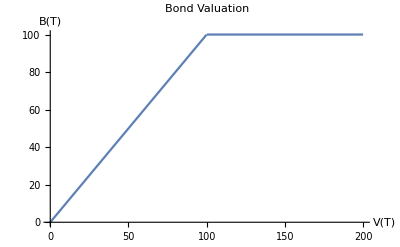

The equity at expiry is

E(T)=max[V(T)-K,0]

And for the same example above, the equity valuation is

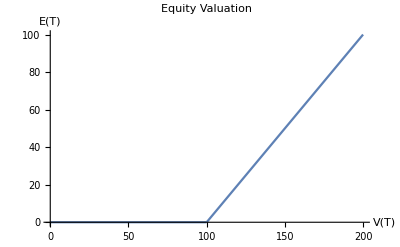

Now assume that the company’s valuation follows a constant coefficient geometric Brownian motion

ⅆV(t)=μ V(t)ⅆt+σ V(t)ⅆW(t)

Thus, the value of the equity is determined by the Black-Scholes formula for a long call option.

E(t)=P(t|σ,K,T,r)

And the value of the bond is a short put option plus a discounted cash position.

B(t)=ⅇ^(-r t)K-C(t|σ,K,T,r)

Also, the value of the company at time t is

V(t)=E(t)+B(t)

### Example

```mathematica
(* Expected Return *)
nM=0.07;
(* Volatility *)
nS=0.2; 
(* Loan Due *)
nT=5; 
(*Risk Free Rate *)
nR=0.01; 
(* Loan Value *)
nK=7000000; 
(* Company Valuation *)
nV=10000000;
```

```mathematica
(* Loan Valuation without Credit Risk *)
nZ=ⅇ^(-nR nT)nK
```

6.65861×10^6

```mathematica
(* Loan Valuation *)
nB=ⅇ^(-nR nT)nK-FinancialDerivative[{"European","Put"},{"StrikePrice"->nK,"Expiration"->nT},{"InterestRate"->nR,"Volatility"->nS,"CurrentPrice"->nV}]
```

6.30384×10^6

```mathematica
(* Effect of Credit Risk *)
nZ-nB
```

354768.

```mathematica
(* Equity Valuation *)
nE=FinancialDerivative[{"European","Call"},{"StrikePrice"->nK,"Expiration"->nT},{"InterestRate"->nR,"Volatility"->nS,"CurrentPrice"->nV}]
```

3.69616×10^6

```mathematica
(* Company Valuation Check *)
nB+nE
```

1.×10^7

### Default Probability

We know from Itô’s lemma that

ⅆlog[V(t)]=(μ-σ^2/2) ⅆt+σⅆW(t)

Thus, given the initial condition V(0) and integrating

log[V(t)]=log[V(0)]+(μ-σ^2/2) T+σ W(T),    W(T)\[Distributed]N[0,√T]

Using the actual expected return yields the real default probability

P[V(T)<K]=P[log V(T)<log K]=F_Normal[(log[K/V(0)]-(μ-σ^2/2) T)/(√(σ T))]

```mathematica
CDF[NormalDistribution[],(Log[nK/nV]-(nM-nS^2/2)nT)/(nS √nT)]
```

0.0874595

Using the risk free return yields the risk neutral default probability

log[V(t)]=log[V(0)]+(r-σ^2/2) T+σ W(T),    W(T)\[Distributed]N[0,√T]

P[V(T)<K]=P[log V(T)<log K]=F_Normal[(log[K/V(0)]-(r-σ^2/2) T)/(√(σ T))]

```mathematica
CDF[NormalDistribution[],(Log[nK/nV]-(nR-nS^2/2)nT)/(nS √nT)]
```

0.246437

### Credit Spread

Another important measure is the credit spread of the bond; i.e., how much the bond yield must increase due to the credit risk of the firm.

Consider a zero coupon bond with prices X, with expiry T and face K. The yield satisfies

X=Exp[-y_XT]K

Taking the log of both sides solving for the yield gives us

y_X=-1/Tlog[X]+log[K]

Thus, the yield spread δ between the risky bond B in the Merton model and a corresponding riskless bond Z is

δ≡y_B-r=-1/T(log[B]-log[Z])

The spread is 109 basis points (1.09%).

```mathematica
nδ=- 1/nT Log[nB/nZ]
```

0.0109503

## Extending the Merton Model

The Merton model, although it does capture many important aspects of credit risk, makes some questionable assumptions. We already know that the constant coefficient geometric Brownian motion can be a poor approximation. The entire debt of the company is modeled by a single zero coupon bond. The default event is modeled to happen at a fixed arbitrary point at time T. The default event is a binary outcome with no provisions for workouts or capital restructuring.

One possible enhancement that will be examined in more detail here is the possibility that default may occur at any point 0≤t≤T. Let 0≤D denote a default trigger. If the value of the firm at any point is V(t)<D, then a default is triggered.

If D<K, then the investors are willing to give the company some leeway with perhaps the hope that the company will be able to grow sufficiently in the future to pay off the debt. If D≥K, the investors are insisting that they hold no risk and as soon as the company appears in danger of default the bond must be paid off. In general, D<K is the more common assumption in which bond holders are exposed to some risk.

As a further extension, the trigger can be time dependent, D(t), such that D(0)>E(0) and D(t)→K as t→T.

### Option Based Solution

For D<K we can model the equity as one type of a barrier option, specifically a down-and-out call. In a down-and-out barrier option the spot price starts above barrier D and the option becomes null and void if the spot falls below the barrier. See https://en.wikipedia.org/wiki/Barrier_option.

Here is FinancialDerivative[ ] for the option in question

```mathematica
FinancialDerivative[{"BarrierDownOut","European","Call"}]
```

{{StrikePrice,Expiration,Barrier,Rebate},{CurrentPrice,Dividend,Volatility,InterestRate}}

Consider our earlier example with D=$6 million.

```mathematica
(* Expected Return *)
nM=0.07;
(* Volatility *)
nS=0.2; 
(* Loan Due *)
nT=5; 
(*Risk Free Rate *)
nR=0.01; 
(* Loan Value *)
nK=7000000; 
(* Company Valuation *)
nV=10000000;
(* Default Barrier *)
nD=6000000;
```

The equity can be modeled as a down-and-out barrier call option.

```mathematica
nEDownOut=FinancialDerivative[{"BarrierDownOut","European","Call"},{"StrikePrice"->nK,"Expiration"->nT,"Barrier"->nD},{"CurrentPrice"->nV,"Volatility"->nS,"InterestRate"->nR}]
```

3.58861×10^6

Our original equity valuation was

```mathematica
nE
```

3.69616×10^6

As expected, given that we now allow for  the possibility of an early default, the equity is worth less: $3.589 million versus $3.696 million from our earlier example.

### Other Solution Approaches

A barrier option is another path dependent option, as were the Asian and lookback options which we studied in previous classes. The down-and-out call with a fixed barrier D can be solved analytically. More complicated cases are challenging; e.g., making the barrier time dependent, D(t). In such cases we need to resort to lattice based methods or Monte Carlo simulation.

### Other Complications

Rather than modeling the debt as a zero coupon bond, we could model it as a standard coupon paying bond. Again, introducing this feature makes the option path dependent. In general, changes made to the original Merton model to make it realistic almost always create path dependencies.

## The Poisson Intensity Model

The Merton model is structural; i.e., it uses the internal capital structure of the firm to model credit risk using options theory. There are alternatives, general covered under the term intensity models, which use market data directly to characterize credit risks. The primary observable which reflects such risks are the bond spreads.

As an alternative to the Merton model, the reduced form intensity model uses market data, specifically credit spreads, to model defaults. It starts out assuming that defaults occur randomly, independently, and without warning from among a large population of debtors. As the probability in which a default occurs in a unit of time p→0 and the size of the population n→∞ such a situation approaches a Poisson process. Thus, the Poisson distribution is a limiting case of the binomial distribution. For details on the limiting process see https://en.wikipedia.org/wiki/Poisson_limit_theorem. For mathematical details on the Poisson process and its applications see https://en.wikipedia.org/wiki/Poisson_point_process.

### Poisson Processes

The PDF of a Poisson distribution with rate parameter λ is

f_Poisson[x|λ]=(ⅇ^-λ λ^x)/(x!),    x≥0

The Poisson distribution is a discrete distribution, e.g., with λ=5 the PDF is

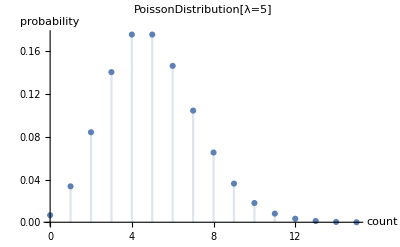

Events arrive at an average rate of λ. The Poisson distribution is widely used in, for example, queuing theory where it is used to model the arrival of customers at a service facility. Here we will use the rate λ as the intensity and assume that the probability of an event A in a small interval Δ is

P[A∈[t,t+Δ]]=λ Δ+o(Δ)

The “little o” notation means that the probability that more than one event occurs in the interval is o(Δ)and goes to zero faster than Δ (see https://en.wikipedia.org/wiki/Big_O_notation).

An important estimate is the probability that a default event does not occur within an interval of time t. This is called the survival probability. Note that we are usually interested in working with risk neutral probabilities.

### Default Model

Consider an interval [0,t] divided into n subintervals of size Δ; i.e., Δ=t/n. The survival probability over the subinterval Δ is 1-λ Δ=1-λ t/n. The probability q(t) of no event over all of the subintervals is (1-λ t/n)^n. Now in the limit as n→∞

q(t)=ⅇ^(-λ t)

It is interesting that the probability above has the same functional form as a continuous time interest rate calculation with the intensity λ instead of r in the exponent.

The probability that an event does occur at some time τ∈[0,t] is

Prob[0≤τ≤t]=1-ⅇ^(-λ t)

The value Z of a riskless zero at time 0≤t≤T with face F and risk free rate r is

Z=ⅇ^(-r T)F

If the bond is subject to default, then the value of the bond B is the expected payoff under the risk neutral measure Q, discounted back to the present. Note that q(T) is the risk neutral survival probability.

B=ⅇ^(-r T)𝔼_Q[payoff]=ⅇ^(-r T)q(T)F=ⅇ^(-(r+λ)T)F

The value of λ tells us how much to increase the yield to account for the increased risk from a default. It is called the short-term credit spread.

### Time Dependence

As with the Merton model, the intensity model has many obvious extensions to make it more representative of a real default process. The most obvious is to make λ time dependent. The default intensity will vary with both the state of the debtor and the conditions in the larger economy. That time dependence can be either deterministic or stochastic. A Poisson process whose intensity λ is not constant is called inhomogeneous.

For a deterministic λ(t) the survival probability can be thought of the limit of the discrete estimate with Δ=T/n

q(t)=lim_(Δ→0) [(ⅇ^(-λ(Δ)))(ⅇ^(-λ(2 Δ)))…(ⅇ^(-λ(n Δ)))]=lim_(Δ→0) [exp[∑_(i=1)^n λ (i Δ)]

which is the integral

q(t)=exp[-∫_0^t λ(s)ⅆs]

If we also have a time dependent short rate curve r(t) then the valuation follows logic similar to that for a constant intensity rate.

B=𝔼[exp[-∫_0^T λ(s)ⅆs]F]=exp[-∫_0^t r(s)ⅆs]q(T)F=exp[-∫_0^t (r(s)+λ(s))ⅆs]F

If the intensity is stochastic, the above are easily generalized. In some cases we can find a closed form solution to the integrals above. If not, we can use lattice methods or Monte Carlo simulations to average over a number of sample paths.

#### Partial Settlements

We have generally assumed that in the event of a default the bondholders receive nothing. In practice this is often not so. If instead the bondholders receive a partial amount f<F then the risk neutral expected value is

B=ⅇ^(-r T)𝔼_Q[payoff]=ⅇ^(-r T)(q(T)F+(1-q(T)f))=ⅇ^(-(r+λ)T)F+(ⅇ^(-r T)-ⅇ^(-(r+λ)T))f

## Bond Credit Rating

Purchasers of bonds are normally not equipped to make judgements about the credit worthiness of a bond and depend on rating agencies to organize bonds into distinct credit categories. See https://en.wikipedia.org/wiki/Bond_credit_rating.

Investors in bonds rely on rating agencies to help guide them in their investment decisions. These agencies rate bonds into predefined categories based on decreasing levels of credit worthiness. Each such agency uses a combination of proprietary analytical and statistical methods. In practice, however, ratings tend to be consistent across the major agencies.

A bond’s yield is determined by the market; however, how a bond is rated by major rating agencies has a huge impact on the market. All else being equal, the better the rating, the lower the yield. The three major rating agencies are Standard & Poors-Dow Jones (S&P), Moody’s, and Fitch.

For example, consider the ratings given to investment grade bonds by Standard & Poors (S&P):

"S&P Investment Grade"
"Highest Quality" | "AAA"
"High Quality" | "AA"
"Upper Medium Grade" | "A"
"Medium Grade" | "BBB"

Many institutions are limited by law or their own internal policies from investing in non-investment grade bonds. The S&P ratings for those bonds are

"S&P Non-Investment Grade"
"Lower Medium" | "BB"
"Low Grade" | "B"
"Poor Quality" | "CCC"
"Speculative" | "CC"
"May Default" | "C"
"In Default" | "D"

The non-investment grade bonds, often called junk bonds, have the highest yields and the greatest risk.

These ratings have not been without their controversies. The subprime mortgage crisis was a component of the 2008 market crash. Many feel that its effects were exacerbated because the ratings agencies used inadequate methods to rate many collateralized debt obligations (CDOs), especially CDOs^2 which are CDOs composed from other CDOs.. See https://en.wikipedia.org/wiki/Collateralized_debt_obligation and https://en.wikipedia.org/wiki/CDO-Squared.

## Idiosyncratic and Systematic Default Risk

Bonds and other forms of debt have both idiosyncratic and systematic risk. These can be used to improve statistical efficiency of estimates of default risk for individual bonds and better estimate the diversification benefits of a portfolio of bonds.

With stocks, for example, we know that some risks are idiosyncratic in that they are tied to a particular firm and some are systematic in that they are reflective of the broader economic environment. We saw in earlier lectures how these effects can be captured in a factor model.

The models so far have dealt with the default risk of an individual debtor. However, a firm’s risk of default is also subject to idiosyncratic and systematic influences. As came be seen below from the default history of the high-yield default risk, this systematic default risk varies over time and appears to be influenced by overall debt levels.

-Graphics-

Source: https://www.zerohedge.com/news/2018-03-18/yet-another-chart-screams-look-out

Decomposing the default risk into its idiosyncratic and systematic components is critical if we are to understand the default risks associated with, for example, a bond portfolio. There are a number of approaches to modeling portfolio-level default risks which are beyond the scope of this class. As a simple example, we might base the systematic risk of a given bond’s default based on its credit rating and then fold in idiosyncratic measures to adjust it based on firm specifics.

## Credit Derivatives

The credit markets are immense and complex. Associated with a wide variety of credit instruments is a an even more complex array of derivative instruments. We provide an overview of the most common forms.

### Credit Default Swaps (CDSs)

A credit default swap is a form of insurance. The buyer of the swap agrees to make regular payments (usually quarterly) to the seller of the swap. Most commonly, in the event of a default the buyer surrenders the bond to the seller and receives from the seller the face amount of the bond. Although the bond is in default, the seller may have an opportunity to recover some portion of value.

-Graphics-   -Graphics-

Source: https://en.wikipedia.org/wiki/Credit_default_swap.

With normal insurance the purchaser of the insurance must have an “insurable interest” in the event being insured against. You can take out fire insurance on your house but you can’t take out the same on your neighbors. CDSs and associated derivatives have no such require. Thus, their sale or purchase represent a means for playing the credit markets. They are also attractive because they can be easily leveraged through borrowing—of course with a corresponding increase in risk.

One method of setting a value to a swap is to set the PV of the protected bond equal to the PV of the bond’s without protection plus the PV of the annuity. Because a possible default the present value of these elements are usually evaluated under the risk neutral measure over a lattice.

In addition to CDSs, there are forwards and options on CDSs (derivatives whose underlying is itself a derivative) that are similar to the corresponding contracts for commodities and stocks.

### Total Return Swaps (TRSs)

Total return swaps (TRSs) are used to hedge out both credit and market risk. The buyer of the protection in addition to receiving the interest from the underlying receives from the seller of the protection an interest payment which is typically a premium over LIBOR or similar base rate plus compensation for any market loss associated with the underlying. The seller of the protection receives any increase in value of the underlying and the underlying’s interest payments.

-Graphics-

Source: https://en.wikipedia.org/wiki/Total_return_swap.

This can be viewed as the protection seller buying the bond on credit and receiving the interest payments from the bond while paying the a “fixed” interest payment to cover the loan.

### Collateralized Debt Obligations (CDOs) and Mortgage Backed Securities

Collateralized debt obligations (CDOs) and mortgage backed securities (MBSs) are trusts in which a number of debt instruments, typically of like type, are placed into a trust. The cash flows from that trust are then broken out into several tranches. Usually, these tranches are identified by how defaults withing the trust are handled. At the top an AAA (triple-A) tranche does not suffer defaults until such losses have been absorbed by least senior tranches. At the bottom an equity tranche must suffer all of the defaults until its share of payments is exhausted.

In most instances the more senior tranches come with a guaranteed interest payment, with the less senior trusts forced to sacrifice to maintain that guarantee. The CDO is said to be busted if enough defaults occur such that the cash flows in the trust are not sufficient to cover these guarantees. Under the law of one price, the total of all tranches of the CDO equals the value of the underlying trust.

-Graphics-

Source: https://en.wikipedia.org/wiki/Collateralized_debt_obligation.

The actual contract which dictates how the cash flows of the trust are to be distributed can be extremely complex. The tranches above can be further split. For example, with MBSs the interest payments and principal payments may be split into separate streams. If a mortgage is prepaid, the holder of the principal tranche receives all of that mortgage’s value as a lump sum and the holder of the interest tranche stops receiving that mortgage’s interest payments. On a default, both principal and interest cash flows of the mortgage are lost.

More complicated arrangements exist; e.g., the interest tranche on variable rate mortgages may be itself split into fixed rate and variable rate tranches. How this is done varies; e.g., the variable rate tranche receives payments only if the interest rate payable on the mortgage rises above the level of the guaranteed fixed rate tranche. Other means of splitting the interest payment cash flows exist.

Even stranger the CDO-squared (CDO^2) where a new CDO is created by combining the tranches of other CDOs. This is most often done to produce additional AAA tranches which are demand by various financial institutions. Of course, such a CDO^2 is constructed from the less senior tranches of other CDOs so attempting to create a AAA tranche from them is hardly straightforward. During the 2007-2008 subprime mortgage crisis many of these CDO^2 did not behave as promised despite the evaluations by bond rating firms whose rankings turned out to be highly optimistic. See https://en.wikipedia.org/wiki/Subprime_mortgage_crisis for more background.